### Determine (1) which models are identifiable for which experimental designs, and (2) what the volume of their parametric domain is given the constraints imposed on the expected count of prey eaten

```mathematica
Clear["Global`*"]

AbundSeries="GoldenRatio";

SetDirectory[FileNameJoin[{NotebookDirectory[],"results/"}]] ;
DumpGet["Models.mx"]
modelNames=(Trace@{H1,LR,BWL1,     
H2,MM,HV,AG,GI, GIA, GB, HT,HT2, H3,AGK, A1, A3, SH,      
BD, CM, AA, BWL2, H3R, A2, HLB, MH, W, TTA, SBB,SSS,    
BDOR, CMOR, AAOR, SN1, SN2})[[All,1]][[1;;Length[models]]]
```

```mathematica
GetParams[model_]:=DeleteDuplicates@Cases[model,Except[Ν|P|T|ⅇ,_Symbol] ,∞]

AllIdentifiable[model_,Νvals_,Pvals_]:=
AllTrue[NullSpace[
Transpose[ArrayReshape[
Flatten[Grad[model,GetParams[model]]/.Ν->Νvals/.P->Pvals],
{Length[GetParams[model]],Length[Νvals]*Length[Pvals]}]]
],TrueQ[#==0] &]
```

```mathematica
logGRSpace[a_,b_,n_]:=Round[GoldenRatio^Range[a,b,(b-a)/(n-1)]]

PreyVals[n_,PreyMax_,AbundSeries_]:=
Which[
AbundSeries=="GoldenRatio",
logGRSpace[2,Log[GoldenRatio,PreyMax]+3,n],
AbundSeries=="Arithmetic",
Round[Range[3,Max[logGRSpace[2,Log[GoldenRatio,PreyMax]+3,n]],(Max[logGRSpace[2,Log[GoldenRatio,PreyMax]+3,n]]-3)/(n-1)]]
]
PredVals[n_,PredMax_,AbundSeries_]:=
If[n==1,
{1}, (* If only a single level is requested, specify a single predator individual *)
Which[ (* Otherwise, determine predator levels according to GoldenRatio or Arithmetic series beginning with 1 predator individual *)
AbundSeries=="GoldenRatio",
logGRSpace[0,Log[GoldenRatio,PredMax]+1,n], 
AbundSeries=="Arithmetic",
Round[Range[1,Max[logGRSpace[0,Log[GoldenRatio,PredMax]+1,n]],(Max[logGRSpace[0,Log[GoldenRatio,PredMax]+1,n]]-1)/(n-1)]]
]]
```

```mathematica
ParamIdent[
ModelAbb_,
AbundSeries_]:=
Module[
{
PreyMinLevels=5, 
PreyMaxLevelsVar=10,
PredMinLevels=1, 
PredMaxLevelsVar=5
}
,
Flatten[
ParallelTable[
Flatten[{
Max[PreyVals[i,Fibonacci[i],AbundSeries]], (* Maximum prey level *)
Max[PredVals[j,Fibonacci[j],AbundSeries]], (* Maximum pred level *)
Length[PreyVals[i,Fibonacci[i],AbundSeries]], (* Number of prey levels *)
Length[PredVals[j,Fibonacci[j],AbundSeries]], (* Number of pred levels *)
AllIdentifiable[
ModelAbb,
PreyVals[i,Fibonacci[i],AbundSeries],
PredVals[j,Fibonacci[j],AbundSeries]]
}],
{i, PreyMinLevels,PreyMaxLevelsVar},
{j,PredMinLevels,PredMaxLevelsVar}
],
1]
]
```

```mathematica
ReshapeData[data_]:=Flatten[SplitBy[data,Part[#,1]&][[All,All,{1,2,5}]],1];
```

```mathematica
square[in_,out_:Black,size_:11]:=Graphics[{in,EdgeForm[{AbsoluteThickness[1],out}],Rectangle[]},PlotRangePadding->0,ImageSize->size];

MyListPlot[
data_,
plotlabel_,
axislabels_]:=
ListPlot[Transpose@{ReshapeData[data][[All,{1,2}]]},
PlotMarkers->{square[Black],square[White]}[[Boole[ReshapeData[data][[All,3]]]+1]],
PlotStyle->Black,
Frame-> True,
FrameLabel-> axislabels,
ImagePadding->{{60,5}, {40, 30}},
PlotRangeClipping->False,
PlotRangePadding-> {Scaled[0.05],Scaled[0.05]},
Epilog->{Text[Style[plotlabel,14],Scaled[{0.5,1.1}]]}
]
```

```mathematica
AxisFontSize=12;
cm = 72/2.54;

axislabelXY={
Style["N_max",AxisFontSize],
Style["P_max",AxisFontSize]};
```

#### Apply to each model

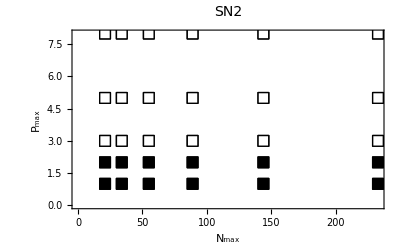

```mathematica
pSN2=MyListPlot[ParamIdent[SN2,AbundSeries],"SN2",axislabelXY]
```

```mathematica
AllModels=Table[MyListPlot[ParamIdent[models[[i]],AbundSeries],modelNames[[i]],axislabelXY],{i,1,Length[models]}];
```

```mathematica
IdentifiablePlot=
Legended[
GraphicsGrid[
ArrayReshape[AllModels,{9,4},""],
Spacings->{0,-8}],
Placed[
SwatchLegend[
{1,2},
{"Identifiable","Non-identifiable"},
LegendMarkers->{square[White],square[Black]},
LegendLayout->"Row",
LabelStyle->19 ],
Above]];
Export["../../Figs/Param_Identiability.pdf",Show[IdentifiablePlot,ImageSize-> 40 cm]];
```